## ATLAS Signal region and Constraints from LHC

```mathematica
SetDirectory[NotebookDirectory[]];
ProjectDirectory="/Users/yoshi/Dropbox/Study_D/projects/z2j/";
```

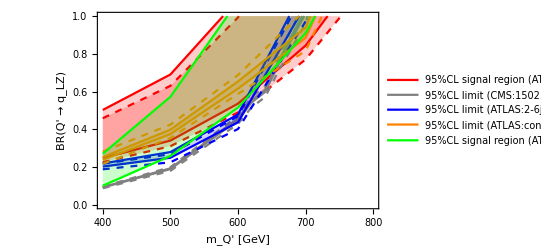

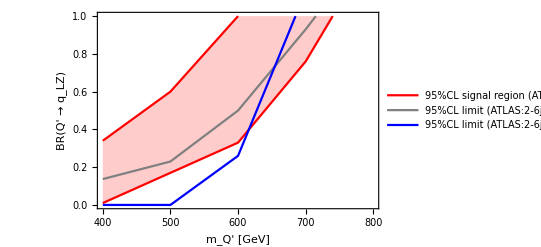

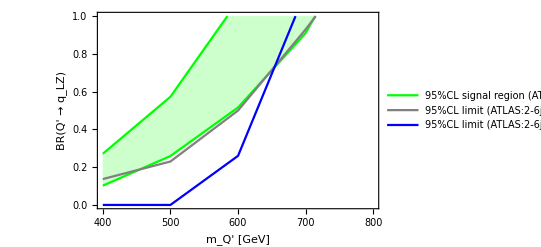

Export::nodir: Directory TraditionalForm`"/Users/yoshi/Dropbox/Study_D/projects/z2j/draft/figures/" does not exist.

Export::noopen: Cannot open TraditionalForm`"/Users/yoshi/Dropbox/Study_D/projects/z2j/draft/figures/limit.pdf".

Syntax::sntx: Invalid syntax in or before "**** Unable to open the initial device, quitting."
                                             ^
     (line 1 of "!/opt/local/bin/pdf2ps /Users/yoshi/Dropbox/Study_D/projects/z2j/draft/figures/limit.pdf
     /Users/yoshi/Dropbox/Study_D/projects/z2j/draft/figures/limit.eps").

ATLAS Signal region and constraints from other LHC analyses in the BR(Q' ¥rightarrow q_L Z) vs. VLQ mass plane. The red region shows the 95%CL ATLAS signal region, while gray- and blue-shaded regions are 95%CL constraint from the CMS on-Z SUSY search and ATLAS 2-6 jet +E_T^{¥rm miss} searches, respectively.

```mathematica
(* signal region from ATLAS 2lepton +2>=jets +MET *)
(*list={{100,0.1},{150,32.054},{200,87.544},{300,90.177},{400,68.944},{500,36.059},{600,15.068},{700,5.673}};*)
(*list={{200,86.609,29.6},{300,126.596,29.6},{400,75.578,29.6},{500,40.52,29.6},{600,16.03,29.6},{700,6.154,29.6}};*)
(* LO *) (* {M_DM, S, S95} for BRZ = 1 *)
LOlist={{200,92,29.6},{300,91.387,29.6},{400,67.099,29.6},{500,36.228,29.6},{600,14.674,29.6},{620,12.112,29.6},{640,10.038,29},{660,8.209,29.6},{680,6.773,29.6},{700,5.583,29.6},{720,4.598,29.6},{740,3.785,29.6},{760,3.132,29.6}};
(* NLO *)
NLOlist={{400,110.222,29.6},{500,58.374,29.6},{600,23.162,29.6},{700,9.567,29.6},{800,3.708,29.6}};
(* {M_DM, S, dS, S95} for BRZ = 1 *)
NNLOlist={{400,117,6,29.6},{500,62,3,29.6},{600,25,1,29.6},{700,10.1,0.6,29.6},{800,4.1,0.3,29.6}};
(* test run checking NNLOlist *)
NNLOlist2={{400,128.816,9.686,29.6},{500,63.1,4.12,29.6},{600,26,0.18,29.6},{700,11.528,0.78,29.6},{800,4.599,0.335,29.6}};
(* test2 run checking NNLOlist using explicit z and w decays *)
NNLOlist3={{400,110.35,3.37,29.6},{500,60.77,2.07,29.6},{600,25.32,0.96,29.6},{700,10.16,0.42,29.6},{800,4.064,0.190,29.6}};
list=NNLOlist;
(*limitmean=Table[{list[[i,1]],(18.4/list[[i,2]])^0.25 0.1},{i,1,Length[list]}];
limitupper=Table[{list[[i,1]],(29.6/list[[i,2]])^0.25 0.1},{i,1,Length[list]}];
limitlower=Table[{list[[i,1]],(7.2/list[[i,2]])^0.25 0.1},{i,1,Length[list]}];*)
limitupper1=Table[{list[[i,1]],Sqrt[(18.4+11.2)/list[[i,2]]]},{i,1,Length[list]}];
limitlower1=Table[{list[[i,1]],Sqrt[(18.4-11.2)/list[[i,2]]]},{i,1,Length[list]}];
limitupper2=Table[{list[[i,1]],Sqrt[(18.4+11.2)/(list[[i,2]]1.2)]},{i,1,Length[list]}];
limitlower2=Table[{list[[i,1]],Sqrt[(18.4-11.2)/(list[[i,2]]1.2)]},{i,1,Length[list]}];

(* BR(bp > d Z) + BRW(bp > u w-) = 1 *)
(* Straight forward event generation i.e., p p > bp bp~ *)
limitupperbrz1={{400,0.34},{500,0.6},{600,1},{700,2},{740,2}}; (* 100k *)
limitlowerbrz1={{400,0.01},{500,0.17},{600,0.33},{700,0.76},{740,1}} ;(* 100k *)
(* optimized event generation for signal *)
limitupperbrz2={{400,0.271},{500,0.573},{600,1.08},{700,2},{800,2}}; (* 10k *)
limitlowerbrz2={{400,0.102},{500,0.259},{600,0.516},{700,0.91},{800,1.55}} ;(* 10k *)
(* optimized event generation for signal *)
limitupperbrz2={{400,0.468},{500,0.666},{600,1.09},{700,2},{800,2}}; (* 100k *)
limitlowerbrz2={{400,0.146},{500,0.252},{600,0.474},{700,0.823},{800,1.55}} ;(* 100k *)

plimit=ListPlot[{limitupper1,limitlower1,limitupper2,limitlower2},Joined->True,PlotStyle->{Red,Red,{Red,Dashed},{Red,Dashed}},Frame->True,FrameLabel->{Text@Style["m_Q' [GeV]",17],Text@Style["BR(Q' → q_LZ)",15]},PlotLegends->Placed[{"95%CL signal region (ATLAS:1503.03290)"},After],Filling->{1->{2},3->{4}},PlotRange->{{100,1000},{0,1}}];
plimitbrz=ListPlot[{limitupperbrz1,limitlowerbrz1},Joined->True,PlotStyle->{Red,Red,{Red,Dashed},{Red,Dashed}},Frame->True,FrameLabel->{Text@Style["m_Q' [GeV]",17],Text@Style["BR(Q' → q_LZ)",15]},PlotLegends->Placed[{"95%CL signal region (ATLAS:1503.03290)"},After],Filling->{2->{1}},PlotRange->{{100,1000},{0,1}}];
plimitbrzv2=ListPlot[{limitupperbrz2,limitlowerbrz2},Joined->True,PlotStyle->{Green,Green},Frame->True,FrameLabel->{Text@Style["m_Q' [GeV]",17],Text@Style["BR(Q' → q_LZ)",15]},PlotLegends->Placed[{"95%CL signal region (ATLAS:1503.03290)"},After],Filling->{2->{1}},PlotRange->{{100,1000},{0,1}}];
(*Show[plimit,Graphics[Text[Style["BR(B->bZ) = 1",13],Scaled[{0.85,0.9}]]],
ImageSize->400]*)

(* limit from ATLAS 2-6jet + MET 1405.7875 *)
(*LOlimit={{100,6737.968,1200},{200,1538.35,270},{300,1481.965,270},{400,143.484,35},{500,83.28,35},{600,44.09,35},{700,18.772,35}};*)
LOlimit={{400,815.915,270},{500,87.65,35},{600,45.093,35},{700,18.821,35}};
NLOlimit={{400,1173,270},{500,126,35},{600,72,35},{700,30,35}};
NNLOlimit={{400,1330,100,270},{500,140,15,35},{600,80,7,35},{700,33,3,35}};
limit=NNLOlimit;
limit2=Table[{limit[[i,1]],limit[[i,4]]/limit[[i,2]]},{i,1,Length[limit]}];
limit2p=Table[{limit[[i,1]],limit[[i,4]]/(limit[[i,2]]+limit[[i,3]])},{i,1,Length[limit]}];
limit2m=Table[{limit[[i,1]],limit[[i,4]]/(limit[[i,2]]-limit[[i,3]])},{i,1,Length[limit]}];
AnalysisUnc=-0.07;
limitdiff=Table[{limit[[i,1]],limit[[i,4]]/(limit[[i,2]](1+AnalysisUnc))},{i,1,Length[limit]}];
plimit2=ListPlot[{limit2,limitdiff,limit2p,limit2m},Joined->True,PlotStyle->{Blue,{Blue,Dashed},{Blue,Dashed}},Frame->True,FrameLabel->{Text@Style["m_Q' [GeV]",17],Text@Style["BR(Q' → q_LZ)",15]},PlotLegends->Placed[{"95%CL limit (ATLAS:2-6jet+MET)"},After],Filling->{1->{2}},PlotRange->{{100,1000},{0,1}}];

(* BR(bp > d Z) + BRW(bp > u w-) = 1 *)
(*limit={{400,0},{500,0.04},{600,0.14},{700,1}};*)
limit={{400,0},{500,0},{600,0.26},{685,1}}; (* 100k *)
plimitbrz2=ListPlot[limit,Joined->True,PlotStyle->Blue,Frame->True,FrameLabel->{Text@Style["m_Q' [GeV]",17],Text@Style["BR(Q' → q_LZ)",15]},PlotLegends->Placed[{"95%CL limit (ATLAS:2-6jet+MET)"},After],PlotRange->{{400,800},{0,1}}];


(* limit from ATLAS Stop seach with 2 leptons 1403.4853 *)
(*limit={{100,0.1,3.1},{200,57.74,74},{300,8.221,3.1},{400,1.851,5.6},{500,0.757,3.1},{600,0.175,3.1},{700,0.105,3.1}};*)
LOlimit={{400,2.158,5.6},{500,0.076,3.1},{600,0.218,3.1},{700,0.161,3.1}};
limit=LOlimit;
limit2=Table[{limit[[i,1]],limit[[i,3]]/limit[[i,2]]},{i,1,Length[limit]}];
plimit3=ListPlot[limit2,Joined->True,PlotStyle->{Darker[Green]},Frame->True,FrameLabel->{Text@Style["m_Q' [GeV]",17],Text@Style["BR(Q' → q_LZ)",15]},PlotLegends->Placed[{"95%CL limit (ATLAS:Stop search)"},After],Filling->Top,PlotRange->{{100,1000},{0,1}}];


(* limit from atlas_conf_2013_047 *)
(*limit={{100,0.1,3.1},{200,215.656,92.4},{300,170.303,92.4},{400,181.89,81.2},{500,129.522,81.2},{600,70.605,81.2},{700,8.34,15.5}};*)
LOlimit={{400,205.512,81.2},{500,128.453,81.2},{600,75.878,81.2},{700,9.166,15.5}};
NLOlimit={{400,302.291,81.2},{500,189.586,81.2},{600,116.51,81.2},{700,14.67,15.5}};
NNLOlimit={{400,330,43,81.2},{500,210,19,81.2},{600,128,10,81.2},{700,17,2,15.5},{800,8.9,0.9,15.5}};
limit=NNLOlimit;
limit2=Table[{limit[[i,1]],limit[[i,4]]/limit[[i,2]]},{i,1,Length[limit]}];
limit2p=Table[{limit[[i,1]],limit[[i,4]]/(limit[[i,2]]+limit[[i,3]])},{i,1,Length[limit]}];
limit2m=Table[{limit[[i,1]],limit[[i,4]]/(limit[[i,2]]-limit[[i,3]])},{i,1,Length[limit]}];
limitdiffp=Table[{limit[[i,1]],limit[[i,4]]/(limit[[i,2]]1.03)},{i,1,Length[limit]}];
limitdiffm=Table[{limit[[i,1]],limit[[i,4]]/(limit[[i,2]]0.97)},{i,1,Length[limit]}];
plimit4=ListPlot[{limitdiffp,limitdiffm,limit2p,limit2m},Joined->True,PlotStyle->{Orange,Orange,{Orange,Dashed},{Orange,Dashed}},Frame->True,FrameLabel->{Text@Style["m_Q' [GeV]",17],Text@Style["BR(Q' → q_LZ)",15]},PlotLegends->Placed[{"95%CL limit (ATLAS:conf_2013_047)"},After],Filling->{1->{2}},PlotRange->{{100,1000},{0,1}}];

(* BR(bp > d Z) + BRW(bp > u w-) = 1 *)
(*limit4={{400,0.1375},{500,0.31},{600,0.545},{700,0.89},{710,1}}; (* 10k *)*)
limit4={{400,0.1375},{500,0.22},{600,0.545},{687,1}}; (* 100k *)
plimitbrz4=ListPlot[limit4,Joined->True,PlotStyle->Darker[Green],Frame->True,FrameLabel->{Text@Style["m_Q' [GeV]",17],Text@Style["BR(Q' → q_LZ)",15]},PlotLegends->Placed[{"95%CL limit (ATLAS:2-6jet+MET)"},After],PlotRange->{{400,800},{0,1}}];


(* limit from cms_1502.06031 *)
LOlimit={{100,6061.035,107},{200,896.668,20},{300,369.237,20},{400,63.383,7.6},{500,28.518,7.6},{600,11.312,7.6},{620,9.091,7.6},{640,7.628,7.6},{660,6.39,7.6},{680,5.329,7.6},{700,4.511,7.6},{720,3.708,7.6},{740,3.083,7.6},{760,2.594,7.6}};
(*limit={{100,6061.035,107},{200,896.668,20},{300,369.237,20},{400,63.383,7.6},{500,28.518,7.6},{600,11.312,7.6},{700,4.511,7.6},{720,7.6},{740,7.6},{760,7.6}};*)
NLOlimit={{400,86.925,7.6},{500,38.04,7.6},{600,16.709,7.6},{700,7.381,7.6},{800,3.061,7.6}};
NNLOlimit={{400,82.1,4,7.6},{500,40,2,7.6},{600,16.9,0.8,7.6},{620,14.0,0.7,7.6},{640,12.7,0.6,7.6},{660,10.2,0.5,7.6},{680,8.6,0.5,7.6},{700,7.5,0.4,7.6},{800,3.1,0.2,7.6}};
limit=NNLOlimit;
limit2=Table[{limit[[i,1]],limit[[i,4]]/limit[[i,2]]},{i,1,Length[limit]}];
limit2p=Table[{limit[[i,1]],limit[[i,4]]/(limit[[i,2]]+limit[[i,3]])},{i,1,Length[limit]}];
limit2m=Table[{limit[[i,1]],limit[[i,4]]/(limit[[i,2]]-limit[[i,3]])},{i,1,Length[limit]}];
limit2diff=Table[{limit[[i,1]],limit[[i,4]]/(limit[[i,2]]0.98)},{i,1,Length[limit]}];
plimit5=ListPlot[{limit2,limit2diff,limit2p,limit2m},Joined->True,PlotStyle->{Gray,Gray,{Gray,Dashed},{Gray,Dashed}},Frame->True,FrameLabel->{Text@Style["m_Q' [GeV]",17],Text@Style["BR(Q' → q_LZ)",15]},PlotLegends->Placed[{"95%CL limit (CMS:1502.06031)"},After],Filling->{1->{2}},PlotRange->{{100,1000},{0,1}}];

(* BR(bp > d Z) + BRW(bp > u w-) = 1 *)
(*limit={{400,0.21},{500,0.23},{600,0.5},{700,1}}; (* 10k *)*)
limit={{400,0.137},{500,0.23},{600,0.5},{700,0.93},{715,1}}; (* 100k *)
plimitbrz5=ListPlot[limit,Joined->True,PlotStyle->Gray,Frame->True,FrameLabel->{Text@Style["m_Q' [GeV]",17],Text@Style["BR(Q' → q_LZ)",15]},PlotLegends->Placed[{"95%CL limit (ATLAS:2-6jet+MET)"},After],PlotRange->{{400,800},{0,1}}];


(*plotall=Show[{plimit,plimit5,plimit2,plimit4},ImageSize->400,PlotRange->{{400,800},{0,1}}]*)
plotall=Show[{plimit,plimit5,plimit2,plimit4,plimitbrzv2},ImageSize->400,PlotRange->{{400,800},{0,1}}]
plotallBrz=Show[{plimitbrz,plimitbrz5,plimitbrz2},ImageSize->400,PlotRange->{{400,800},{0,1}}]
plotallBrz2=Show[{plimitbrzv2,plimitbrz5,plimitbrz2},ImageSize->400,PlotRange->{{400,800},{0,1}}]
Export[ProjectDirectory<>"draft/figures/limit.pdf",plotall];
<<"!/opt/local/bin/pdf2ps /Users/yoshi/Dropbox/Study_D/projects/z2j/draft/figures/limit.pdf /Users/yoshi/Dropbox/Study_D/projects/z2j/draft/figures/limit.eps"
<<"!rm -rf /Users/yoshi/Dropbox/Study_D/projects/z2j/draft/figures/limit.pdf"
Print[ "ATLAS Signal region and constraints from other LHC analyses in the BR(Q' ¥rightarrow q_L Z) vs. VLQ mass plane. The red region shows the 95%CL ATLAS signal region, while gray- and blue-shaded regions are 95%CL constraint from the CMS on-Z SUSY search and ATLAS 2-6 jet +E_T^{¥rm miss} searches, respectively."]
```